```mathematica
MovingAverageTimeSeries[data:{{_,_}..},windowSize_Integer?Positive]:=Module[{times,values,ts,movingAvg},
(*Extract times and values from input data*)
{times,values}=Transpose[data];

(*Create a TimeSeries object for efficient temporal operations*)ts=TimeSeries[values,{times}];

(*Use MovingMap with Mean for the moving average calculation*)
(*"Fixed" partition ensures we only use available data within the window*)movingAvg=MovingMap[Mean,ts,windowSize,"Fixed"];

(*Return as {time,value} pairs*)
movingAvg["Path"]
]
```

```mathematica
MovingMap[Mean,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5]},3]
```

{1/4 (x_1+x_2+x_3+x_4),1/4 (x_2+x_3+x_4+x_5)}

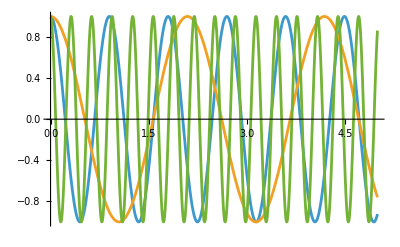

```mathematica
Plot[Re/@{Exp[-I*6.99*t],Exp[-I*3.*t],Exp[-I*20.*t]}//Evaluate,{t,0,5}]
```

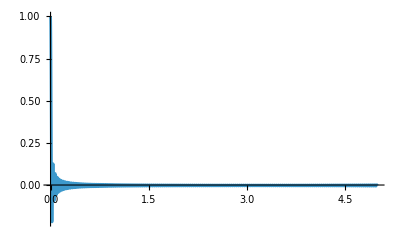

```mathematica
Plot[Total[Re[Exp[-I*#*t]]&/@Range[1,200,1.]]/200,{t,0,5},PlotRange->All]
```

```mathematica
Plot[Total[Re[Exp[-I*#*t]]&/@Range[1,200,1.]]/200,{t,0,5},PlotRange->All]
```

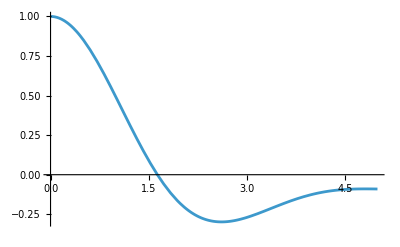

```mathematica
s=RandomVariate[RayleighDistribution[Sqrt[2/Pi]],1000.];
Plot[Total[Cos[#*t]&/@s]/Length[s],{t,0,5},PlotRange->All]
```

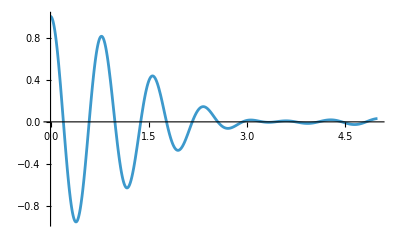

```mathematica
s=RandomVariate[NormalDistribution[8.,0.85],1000.];
Plot[Total[Cos[#*t]&/@s]/Length[s],{t,0,5},PlotRange->All]
```

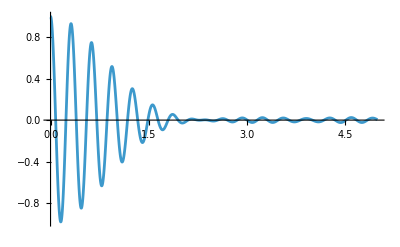

```mathematica
s=RandomVariate[NormalDistribution[20.,1.2],1000.];
Plot[Total[Cos[#*t]&/@s]/Length[s],{t,0,5},PlotRange->All]
```

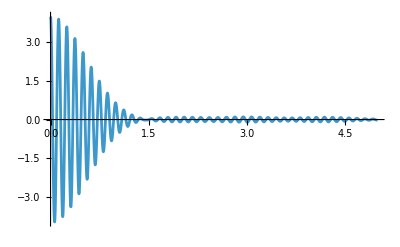

```mathematica
s1=RandomVariate[NormalDistribution[49.,1.5],1000.];
s2=RandomVariate[NormalDistribution[50.,1.5],1000.];
s3=RandomVariate[NormalDistribution[51.,1.5],1000.];
s4=RandomVariate[NormalDistribution[52.,1.5],1000.];
Plot[Total[Cos[#*t]&/@s1]/Length[s1]+Total[Cos[#*t]&/@s2]/Length[s2]+Total[Cos[#*t]&/@s3]/Length[s3]+Total[Cos[#*t]&/@s4]/Length[s4],{t,0,5},PlotRange->All]
```

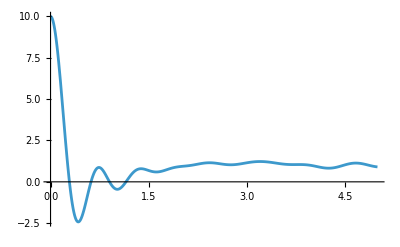

```mathematica
s=Flatten[RandomVariate[NormalDistribution[#,0.6+(#-2)*0.05],1000.]&/@Range[2,10]];
Plot[Total[Cos[#*t]&/@s]/1000.+1.,{t,0,5},PlotRange->All]
```

```mathematica
d=Table[Total[Cos[#*t]&/@s]/Length[s],{t,0,5,0.01}];
```

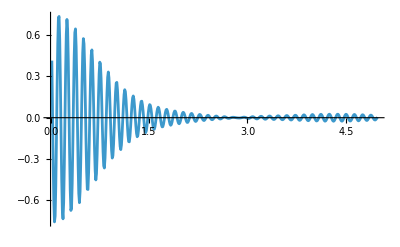

```mathematica
ListPlot[Transpose[{MovingMap[Mean,Range[0,5,0.01],4],MovingMap[Mean,d,4]}],Joined->True,PlotRange->All]
```

```mathematica
Needs["QMB`"]
```

```mathematica
e=Unfold[Sort@RandomReal[{-10,10},2000]]["UnfoldedLevels"];
```

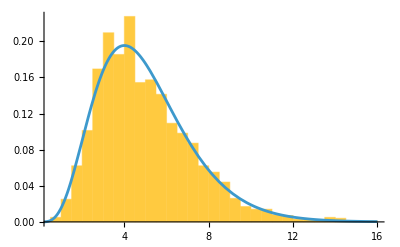

```mathematica
k=5;
Show[
Histogram[Differences[e,1,k],Automatic,"PDF"],
Plot[PDF[GammaDistribution[k,1],s],{s,0,16},PlotRange->All]
]
```

```mathematica
eigenvals=Unfold[Sort[Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[4000]]]]]["UnfoldedLevels"];
```

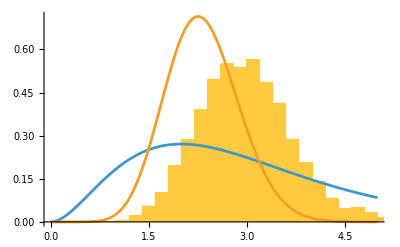

```mathematica
k=3;
Show[
Histogram[Differences[eigenvals,1,k],Automatic,"PDF",PlotRange->{{0,5},All}],
Plot[{PDF[GammaDistribution[k,1],s],GOESpacingDistribution[k,s]}//Evaluate,{s,0,5},PlotRange->All]
]
```

```mathematica
n=L=8;
J=1.;U=10.;(*chaotic regime*)
```

```mathematica
H=BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"EvenParity"];
energies=Unfold[Sort[Chop@Eigenvalues[Normal@H]]]["UnfoldedLevels"];
```

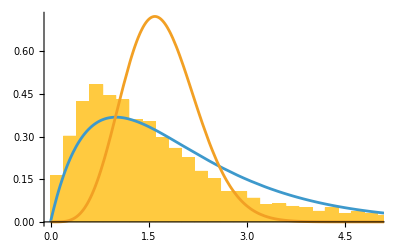

```mathematica
k=2;
Show[
Histogram[Differences[energies,1,k],Automatic,"PDF",PlotRange->{{0,5},All}],
Plot[{PDF[GammaDistribution[k,1],x],GOESpacingDistribution[k,x]}//Evaluate,{x,0,20},PlotRange->All]
]
```

```mathematica
FitPDF[data_List]:=Module[{dist,pdf},(*Step 1:Let Mathematica find the best-fitting distribution*)dist=FindDistribution[data];
(*Step 2:Define the PDF function*)pdf=PDF[dist,#]&;
<|"BestFitDistribution"->dist,"PDF"->pdf,"Mean"->Mean[dist],"Variance"->Variance[dist],"GoodnessOfFitTest"->DistributionFitTest[data,dist,"TestStatistic"],"PValue"->DistributionFitTest[data,dist,"PValue"]|>]
```

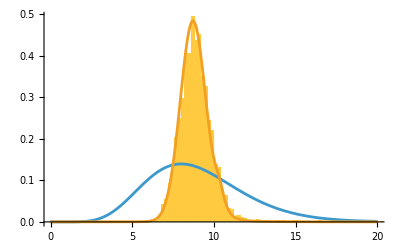

```mathematica
k=9;s=Differences[eigenvals,1,k];
fit=FitPDF[s];
Show[
Histogram[s,Automatic,"PDF",PlotRange->{{0,20},All}],
Plot[{PDF[GammaDistribution[k,1],x],fit["PDF"][x]}//Evaluate,{x,0,20},PlotRange->All]
]
```

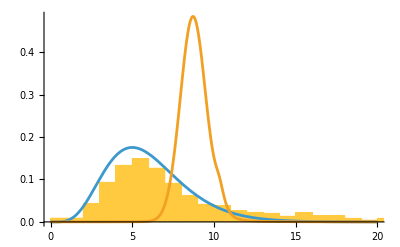

```mathematica
k=9;
Show[
Histogram[Differences[energies,1,k],Automatic,"PDF",PlotRange->{{0,20},All}],
Plot[{PDF[GammaDistribution[6,1],x],fit["PDF"][x]}//Evaluate,{x,0,20},PlotRange->All]
]
```

## Mean level spacing ratio

### Definiciones

```mathematica
Needs["QMB`"]
```

```mathematica
ClearAll[LevelSpacingRatios]
LevelSpacingRatios[eigvals_List,k_Integer:1,reduced_:True]:=
Module[{evals,spacings,ratios},
(*Compute kth-order spacings*)
spacings=Differences[Sort[eigvals],1,k];
(*Compute consecutive ratios*)
ratios=Rest[spacings]/Most[spacings];
(*:Optionally reduce the ratio to (0,1]*)
If[reduced,ratios=Map[Min[#1,1/#1]&,ratios]];

ratios]
```

### Calculos

```mathematica
d=5000;
eigvals=Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[d]]];
```

```mathematica
goe=Table[Mean[LevelSpacingRatios[eigvals,k,False]],{k,1000}];
```

```mathematica
numbers=RandomReal[{-10,10},10000];
```

```mathematica
poisson=Table[Mean[LevelSpacingRatios[numbers,k,False]],{k,1000}];
```

```mathematica
n=L=8;
J=1.;U=1.;(*chaotic regime*)
```

```mathematica
H=BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"EvenParity"];
energies=Sort[Chop@Eigenvalues[Normal@H]];
```

```mathematica
bh=Table[Mean[LevelSpacingRatios[energies,k]],{k,1000}];
```

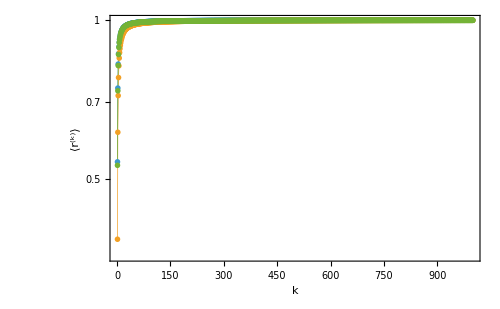

```mathematica
ListLogPlot[{goe,poisson,bh},PlotRange->All,Joined->True,PlotMarkers->{"OpenMarkers", 6},PlotStyle->{Directive[Thickness[0.001]],Directive[Thickness[0.001]]},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm[k],"⟨r^(k)⟩"},ImageSize->500]
```

```mathematica
n=L=8;
J=77.;U=1.;(*regular regime*)
```

```mathematica
H=BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"EvenParity"];
energies=Sort[Chop@Eigenvalues[Normal@H]];
```

```mathematica
bh=Table[Mean[LevelSpacingRatios[energies,k]],{k,1000}];
```

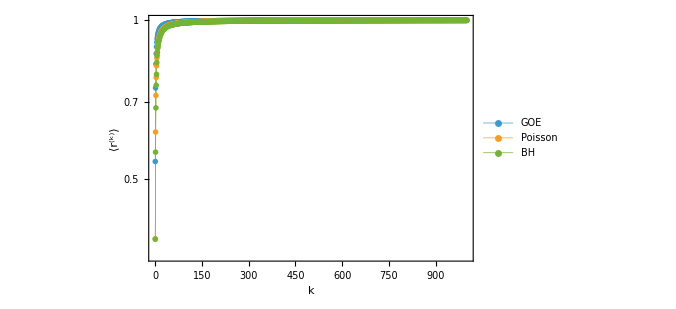

```mathematica
ListLogPlot[{goe,poisson,bh},PlotRange->All,Joined->True,PlotMarkers->{"OpenMarkers", 6},PlotStyle->{Directive[Thickness[0.001]],Directive[Thickness[0.001]]},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm[k],"⟨r^(k)⟩"},PlotLegends->{"GOE","Poisson","BH"},ImageSize->500]
```

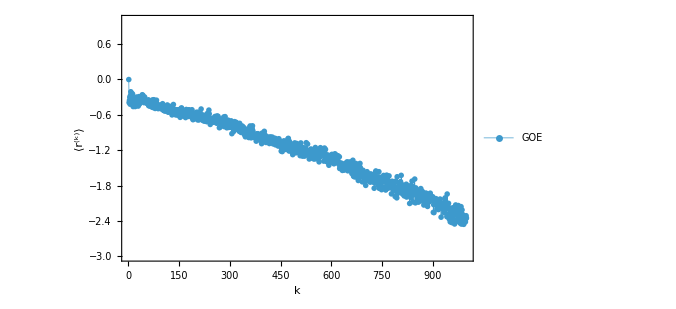

```mathematica
ListPlot[(bh-poisson)/(goe-poisson),PlotRange->{All,{-3,1}},Joined->True,PlotMarkers->{"OpenMarkers", 6},PlotStyle->{Directive[Thickness[0.001]],Directive[Thickness[0.001]]},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm[k],"⟨r^(k)⟩"},PlotLegends->{"GOE","Poisson","BH"},ImageSize->500]
```

```mathematica
n=L=8;
J=2.;U=1.;(*regular regime*)
```

```mathematica
H=BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"EvenParity"];
energies=Sort[Chop@Eigenvalues[Normal@H]];
```

```mathematica
bh=Table[Mean[LevelSpacingRatios[energies,k]],{k,1000}];
```

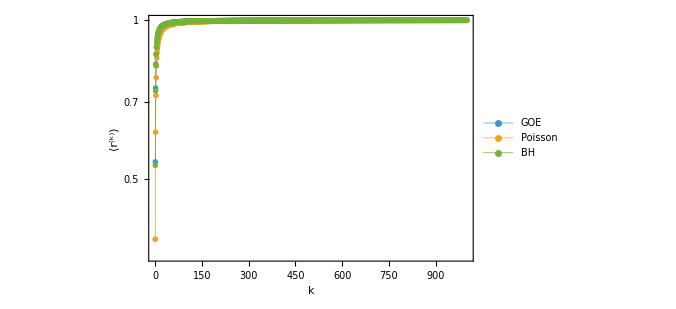

```mathematica
ListLogPlot[{goe,poisson,bh},PlotRange->All,Joined->True,PlotMarkers->{"OpenMarkers", 6},PlotStyle->{Directive[Thickness[0.001]],Directive[Thickness[0.001]]},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm[k],"⟨r^(k)⟩"},PlotLegends->{"GOE","Poisson","BH"},ImageSize->500]
```

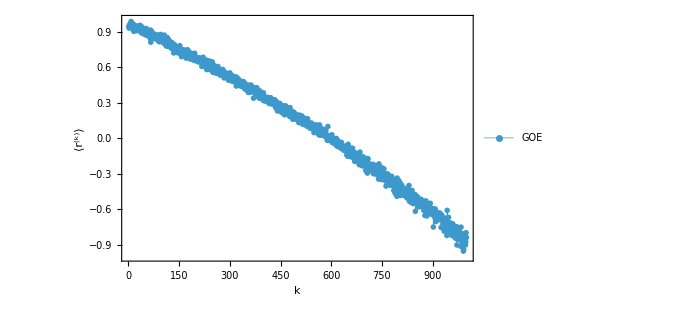

```mathematica
ListPlot[(bh-poisson)/(goe-poisson),PlotRange->{All,{-1,1}},Joined->True,PlotMarkers->{"OpenMarkers", 6},PlotStyle->{Directive[Thickness[0.001]],Directive[Thickness[0.001]]},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm[k],"⟨r^(k)⟩"},PlotLegends->{"GOE","Poisson","BH"},ImageSize->500]
```

```mathematica
n=L=8;
J=3.;U=1.;(*chaotic regime*)
```

```mathematica
H=BoseHubbardHamiltonian[n,L,J,U];
energies=Sort[Chop@Eigenvalues[Normal@H]];
```

```mathematica
bh=Table[Mean[LevelSpacingRatios[energies,k,False]],{k,1000}];
bhTilde=Table[Mean[LevelSpacingRatios[energies,k]],{k,1000}];
```

```mathematica
d=5000;
eigvalsGUE=Eigenvalues[RandomVariate[GaussianUnitaryMatrixDistribution[d]]];
```

```mathematica
d=4000;
eigvals=Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[d]]];
```

```mathematica
goe=Table[Mean[LevelSpacingRatios[eigvals,k,False]],{k,1000}];
goeTilde=Table[Mean[LevelSpacingRatios[eigvals,k]],{k,1000}];
```

```mathematica
gue=Table[Mean[LevelSpacingRatios[eigvalsGUE,k,False]],{k,1000}];
gueTilde=Table[Mean[LevelSpacingRatios[eigvalsGUE,k]],{k,1000}];
```

```mathematica
numbers=RandomReal[{-10,10},5000];
poisson=Table[Mean[LevelSpacingRatios[numbers,k,False]],{k,1000}];
poissonTilde=Table[Mean[LevelSpacingRatios[numbers,k]],{k,1000}];
```

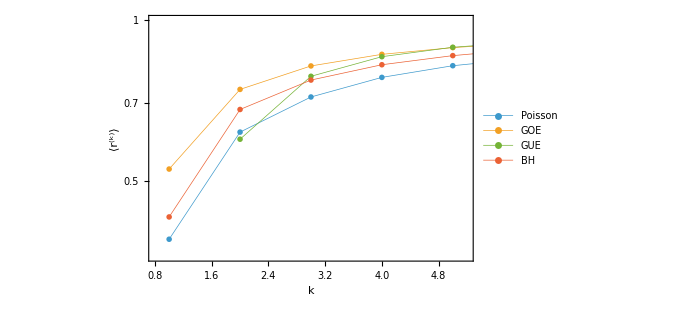

```mathematica
ListLogPlot[{Transpose[{Range[1,1000],poissonTilde[[1;;]]}],goeTilde,Transpose[{Range[2,1001],gueTilde}],Transpose[{Range[1,1000],bhTilde[[1;;]]}]},PlotRange->{{0.8,5.2},All},Joined->True,PlotMarkers->{"OpenMarkers", 6},PlotStyle->{Directive[Thickness[0.001]],Directive[Thickness[0.001]]},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm[k],"⟨r^(k)⟩"},ImageSize->500,PlotLegends->{"Poisson","GOE","GUE","BH"}]
```

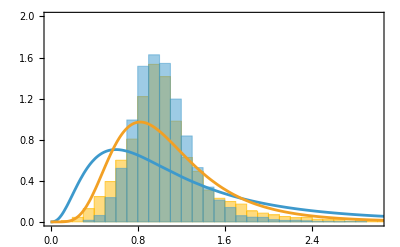

```mathematica
k=4;
Show[
Histogram[{LevelSpacingRatios[numbers,k,False],LevelSpacingRatios[energies,k,False]},Automatic,"PDF",PlotRange->{{0,3},{0,2.}},Frame->True],
Plot[{((2k-1)!*r^(k-1))/(((k-1)!)^2(1+r)^(2*k)),Pnum[r,k+2]//Evaluate},{r,0,10},PlotRange->All]
]
```

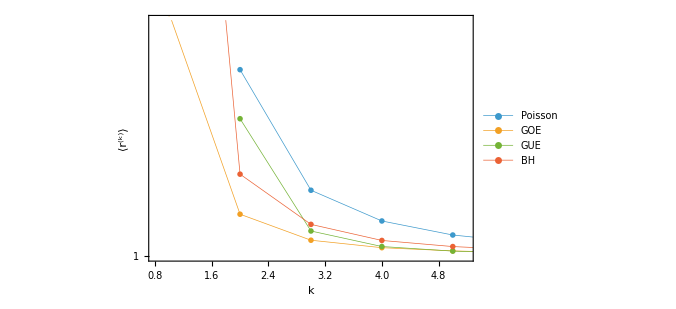

```mathematica
ListLogPlot[{Transpose[{Range[2,1000],poisson[[2;;]]}],goe,Transpose[{Range[2,1001],gue}],Transpose[{Range[1,1000],bh[[1;;]]}]},PlotRange->{{0.8,5.2},{1,1.7}},Joined->True,PlotMarkers->{"OpenMarkers", 6},PlotStyle->{Directive[Thickness[0.001]],Directive[Thickness[0.001]]},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm[k],"⟨r^(k)⟩"},ImageSize->500,PlotLegends->{"Poisson","GOE","GUE","BH"}]
```

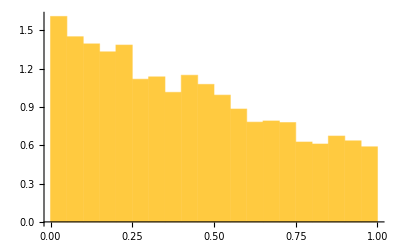

```mathematica
Histogram[LevelSpacingRatios[energies,1],Automatic,"PDF"]
```

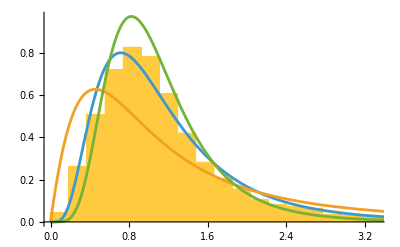

```mathematica
k=6;
Show[
Histogram[LevelSpacingRatios[energies,2,False],Automatic,"PDF"],
Plot[{((2k-1)!*r^(k-1))/(((k-1)!)^2(1+r)^(2*k)),P[r,1],Pnum[r,k]//Evaluate},{r,0,10},PlotRange->All]
]
```

```mathematica
Zβ[1]:=8/27;Zβ[2]:=(4π)/(81 √3);Zβ[4]:=(4π)/(729 √3);
P[r_,β_]:=1/Zβ[β]((r+r^2)^β)/((1+r+r^2)^(1+3/2*β))
```

```mathematica
β=1.;
Pnum[r_,β_]:=Module[{Cβ=(NIntegrate[((r+r^2)^β)/((1+r+r^2)^(1+3/2*β)),{r,0,Infinity}])^-1},Cβ*((r+r^2)^β)/((1+r+r^2)^(1+3/2*β))]
```

```mathematica
NIntegrate[r*Pnum[r,1.],{r,0,Infinity}]
```

1.75

```mathematica
Mean[LevelSpacingRatios[eigvals,1,False]]
```

1.72585

```mathematica
ClearAll[Poisson];
Poisson[r_,k_]:=((2k-1)!*r^(k-1))/(((k-1)!)^2(1+r)^(2*k))
```

```mathematica
Integrate[r*Poisson[r,2.],{r,0,Infinity}]
```

2.

## dfd

```mathematica
d=15000;
eigvals=Catenate@Table[Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[d]]],2];
```

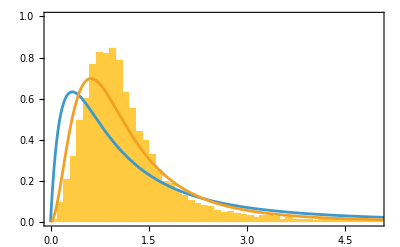

```mathematica
k=2;
Show[
Histogram[LevelSpacingRatios[eigvals,k,False],Automatic,"PDF",PlotRange->{{0,5.},{0,1.}},Frame->True],
Plot[{((2k-1)!*r^(k-1))/(((k-1)!)^2(1+r)^(2*k)),Pnum[r,k]//Evaluate},{r,0,10},PlotRange->All]
]
```

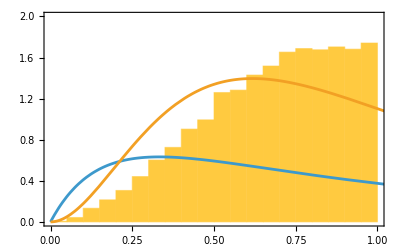

```mathematica
k=2;
Show[
Histogram[LevelSpacingRatios[eigvals,k,True],Automatic,"PDF",PlotRange->{{0,1.},{0,2.}},Frame->True],
Plot[{((2k-1)!*r^(k-1))/(((k-1)!)^2(1+r)^(2*k)),2*Pnum[r,k]//Evaluate},{r,0,10},PlotRange->All]
]
```

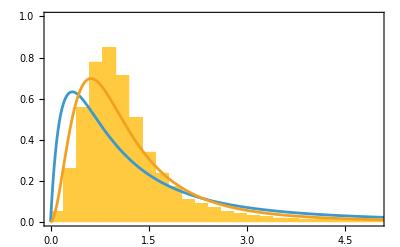

```mathematica
k=2;
Show[
Histogram[LevelSpacingRatios[eigvals,k,False],Automatic,"PDF",PlotRange->{{0,5.},{0,1.}},Frame->True],
Plot[{((2k-1)!*r^(k-1))/(((k-1)!)^2(1+r)^(2*k)),Pnum[r,k]//Evaluate},{r,0,10},PlotRange->All]
]
```